```mathematica
R={c->d,c->e,d->d,a->c,b->a,c->a,e->c}
```

{c→d,c→e,d→d,a→c,b→a,c→a,e→c}

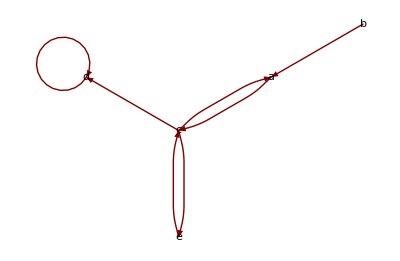

```mathematica
GraphPlot[R,DirectedEdges->True,VertexLabeling->True]
```

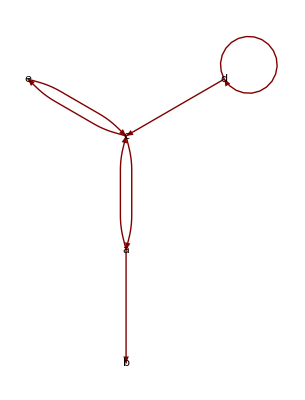

```mathematica
GraphPlot[ReverseGraph[Graph[R]],DirectedEdges->True,VertexLabeling->True]
```

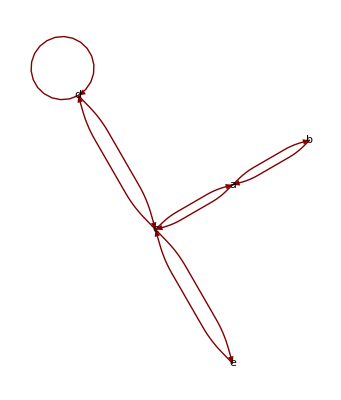

```mathematica
GraphPlot[{c->a,a->b,b->a,a->c,c->d,d->c,e->c,d->d,c->e},DirectedEdges->True,VertexLabeling->True]
```

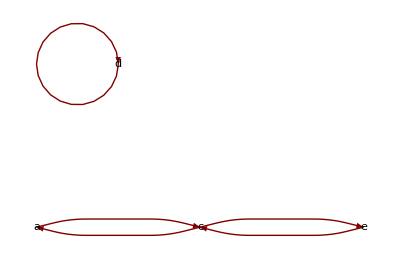

```mathematica
GraphPlot[{a->c,c->a,d->d,e->c,c->e},DirectedEdges->True,VertexLabeling->True]
```